```mathematica
(* Define the sample space and probabilities *)
labels={"Mediterranean Avenue","Oriental Avenue","St. Charles Place","St. James Place","Kentucky Avenue","Atlantic Avenue","Pacific Avenue","Park Place"}

onehouseprofit=Import["one_house.txt", "list"]
twohouseprofit=Import["two_houses.txt", "list"]
threehouseprofit=Import["three_houses.txt", "list"]
fourhouseprofit=Import["four_houses.txt", "list"]
hotelprofit=Import["hotels.txt", "list"]
```

{Mediterranean Avenue,Oriental Avenue,St. Charles Place,St. James Place,Kentucky Avenue,Atlantic Avenue,Pacific Avenue,Park Place}

{0.121704,0.12315,0.122616,0.129494,0.129119,0.124608,0.127145,0.122165}

{0.102867,0.112319,0.113096,0.134176,0.133499,0.131837,0.140511,0.131694}

{0.0737134,0.0974749,0.105595,0.145531,0.151433,0.140557,0.150692,0.135003}

{0.0687817,0.0995063,0.107141,0.155693,0.1525,0.139319,0.148675,0.128384}

{0.0696654,0.101836,0.107477,0.158314,0.152617,0.138816,0.14626,0.125014}

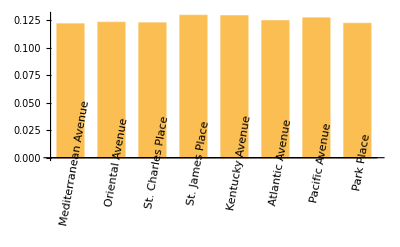

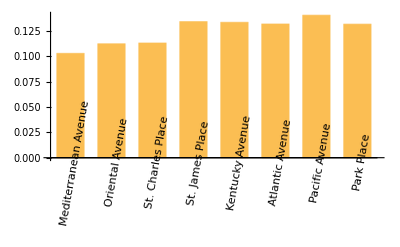

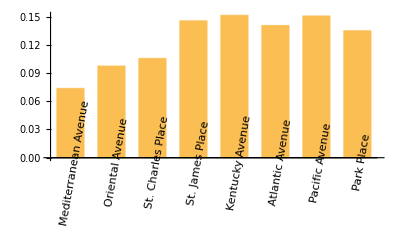

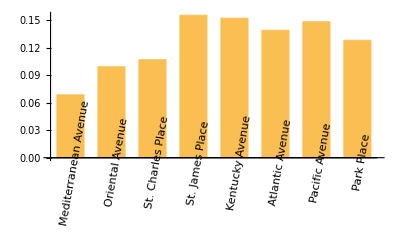

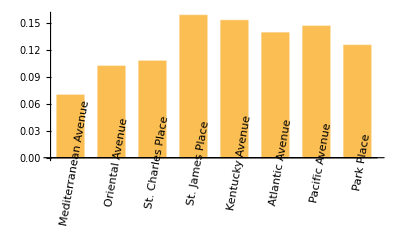

```mathematica
BarChart[onehouseprofit,BarSpacing -> Large, ChartLabels ->Placed[labels, Below, Rotate[#, 80 Degree] &]]
BarChart[twohouseprofit,BarSpacing -> Large, ChartLabels ->Placed[labels, Below, Rotate[#, 80 Degree] &]]
BarChart[threehouseprofit,BarSpacing -> Large, ChartLabels ->Placed[labels, Below, Rotate[#, 80 Degree] &]]
BarChart[fourhouseprofit,BarSpacing -> Large, ChartLabels ->Placed[labels, Below, Rotate[#, 80 Degree] &]]
BarChart[hotelprofit,BarSpacing -> Large, ChartLabels ->Placed[labels, Below, Rotate[#, 80 Degree] &]]
```

```mathematica
(*top five names and probs*)
topfivenames={}
topfiveprobs={}
max=First[First[Position[probabilities,Max[probabilities]]]]
topfivenames=Append[topfivenames,Part[sampleSpace,max]]
topfiveprobs=Append[topfiveprobs,Part[probabilities,max]]
probabilities=Delete[probabilities,max];
sampleSpace=Delete[sampleSpace,max];
```

{}

{}

11

{Jail / Just Visiting}

{0.0522203}

17

{Jail / Just Visiting,Community Chest 2}

{0.0522203,0.0372497}

17

{Jail / Just Visiting,Community Chest 2,Tennessee Avenue}

{0.0522203,0.0372497,0.0360959}

17

{Jail / Just Visiting,Community Chest 2,Tennessee Avenue,New York Avenue}

{0.0522203,0.0372497,0.0360959,0.0342042}

16

{Jail / Just Visiting,Community Chest 2,Tennessee Avenue,New York Avenue,St. James Place}

{0.0522203,0.0372497,0.0360959,0.0342042,0.0340129}

{}

{}

26

{Go to Jail}

{0.}

1

{Go to Jail,Go}

{0.,0.0153969}

1

{Go to Jail,Go,Mediterranean Avenue}

{0.,0.0153969,0.0156845}

{Mediterranean Avenue,Go,Go to Jail}

{0.0156845,0.0153969,0.}

{}

0

Delete::psl: Position specification 8 Chance 1 in {0.024391,0.0244577,0.0246284,0.0248225,0.0250736,0.0254185,0.0256284,0.0258721,0.02582,0.0256523,«30»} is not a machine-sized integer or a list of machine-sized integers.

Delete::psl: Position specification 8 Chance 1 in {Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,«30»} is not a machine-sized integer or a list of machine-sized integers.

Part::pkspec1: The expression {{8 Chance 1,0.206977}} cannot be used as a part specification.

Delete::psl: Position specification 8 {Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,«30»}⟦{{8 Chance 1,0.206977}}⟧ in {0.024391,0.0244577,0.0246284,0.0248225,0.0250736,0.0254185,0.0256284,0.0258721,0.02582,0.0256523,«30»} is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Delete::psl will be suppressed during this calculation.

Part::pkspec1: The expression {{8 {Go,Mediterranean Avenue,Community Chest 1,Baltic Avenue,Income Tax,Reading Railroad,Oriental Avenue,Chance 1,Vermont Avenue,Connecticut Avenue,«30»}⟦{{8 Chance 1,0.206977}}⟧,8 {0.024391,0.0244577,0.0246284,0.0248225,«4»,0.02582,0.0256523,«30»}⟦{«1»}⟧}} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

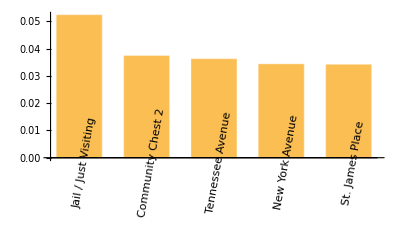

```mathematica
BarChart[topfiveprobs,BarSpacing -> Large, ChartLabels ->Placed[topfivenames, Below, Rotate[#, 80 Degree] &]]
```

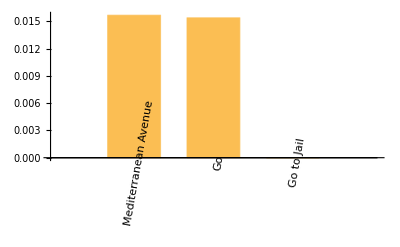

```mathematica
BarChart[bottomfiveprobs, BarSpacing -> Large,ChartLabels ->Placed[bottomfivenames, Below, Rotate[#, 80 Degree] &]]
```

```mathematica
bottomfivenames
```

{Go to Jail,Go,Mediterranean Avenue,Boardwalk,Community Chest 1}

```mathematica
bottomfiveprobs
```

{0.,0.0153969,0.0156845,0.0166057,0.0175326}